```mathematica
Clear["`*"]
SetDirectory[NotebookDirectory[]]
```

C:\Users\shiyi\work\git\work\critical_region\cheby\LPA\v7

```mathematica
(*list0=Flatten[Import["a.dat"]];*)
list=Table[Flatten[Import["./mub0_IR0p01/bdata/b"<>ToString[i]<>".dat"]],{i,1,20}];
```

```mathematica
list2=Table[Rest[list[[i]]],{i,1,20}];
```

```mathematica
ρmin=0;
ρmax=45000;
```

```mathematica
rhoend=0.1;
eqn7=Table[Table[Evaluate[(test=SetPrecision[Sum[list2[[i]][[n]]*Cos[n*ArcCos[(2ρ-ρmin-ρmax)/(ρmax-ρmin)]],{n,1,50}]+1/2 First[list[[i]]],52])],{ρ,0,rhoend,rhoend/200}],{i,1,20}];
sigma=Table[√(2 rho),{rho,0,rhoend,rhoend/200}];
```

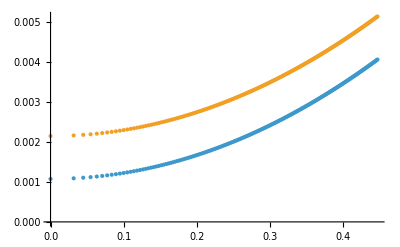

```mathematica
ListPlot[{Transpose[{sigma,eqn7[[1]]}],Transpose[{sigma,eqn7[[2]]}]},PlotRange->All]
```

```mathematica
lT=20;
T=Table[Exp[Log[10^-4]-(Log[10^-4]-Log[100])/20*(i-1)]//N,{i,1,lT}];
```

```mathematica
V1data=Table[eqn7[[i]][[1]],{i,1,20}];
slop=Table[{SetPrecision[Log[T[[i]]/124.69765],90],SetPrecision[Re[FindFit[Transpose[{-Log[T/124.69765],Log[1/√V1data]}][[i;;i+1]],a x+b,{a,b},x][[1]][[2]]],90]},{i,1,lT-1}];
```

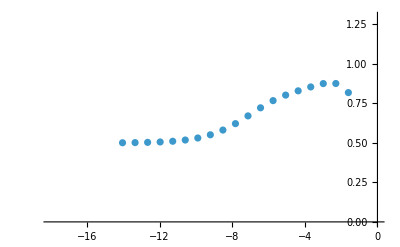

```mathematica
ListPlot[slop,ScalingFunctions->{Automatic,Automatic},PlotRange->{{-18,0},{0.,1.3}}]
```